x | y
1 | 9.75965
2 | 10.1318
3 | 10.0173
4 | 14.2675
5 | 14.5699
6 | 22.5636
7 | 22.7625
8 | 24.876
9 | 25.9721
10 | 31.5594
11 | 35.41
12 | 33.3023
13 | 37.2541
14 | 42.3084
15 | 43.0031
16 | 43.5838
17 | 50.0174
18 | 49.543
19 | 55.4237
20 | 55.5277

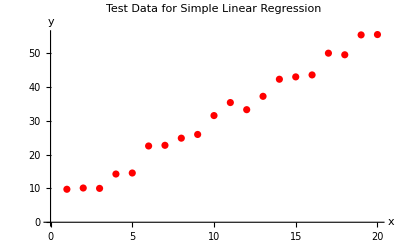

Source | Sum of Squares | df | Mean Square | F-statistic | p-value
Regression | 4409.63 | 1 | 4409.63 | 1320.56 | 2.683055813371×10^-18
Error | 60.1057 | 18 | 3.33921 |  | 
Total | 4469.73 | 19 |  |  |

Fitted regression equation: y = 4.55436 + 2.57508 * x

Intercept→ 4.55436,Slope→ 2.57508

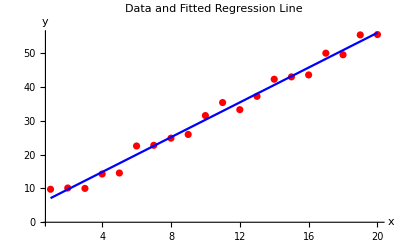

```mathematica
simpleLinearRegression[X_,Y_]:=
Module[{n,XBar,YBar,ssxx,ssxy,ssyy,b1,b0,tss,ssr,sse,dfR,,dfE,msr,mse,fStat,regressionEquation},

(*Length of the data*)
n=Length[X];

(*Calculate means*)
XBar=Mean[X];
YBar=Mean[Y];

(*Calculate variance and covariance*)
ssxx=Total[(X-XBar)^2];
ssxy=Total[(X-YBar) (Y-YBar)];
ssyy=Total[(Y-YBar)^2];

(*Calculate regression coefficients*)
b1=ssxy/ssxx;
b0=YBar-b1*XBar;

(*ANOVA calculations*)
tss=Total[(Y-YBar)^2];ssr=Total[(b0+b1*x-YBar)^2];sse=tss-ssr;dfR=1;dfE=n-2;msr=ssr/dfR;mse=sse/dfE;fStat=msr/mse;

(*ANOVA Table*)
anovaTable=
{{"Source","Sum of Squares","df","Mean Square","F-statistic","p-value"},{"Regression",ssr,dfR,msr,fStat,1-CDF[FRatioDistribution[dfR,dfE],fStat]},
{"Error",sse,dfE,mse,"",""},
{"Total",tss,n-1,"","",""}};
Print[Grid[anovaTable,Frame->All]];

(*Print the regression equation*)
Print[StringForm["Fitted regression equation: y = `1` + `2` * x",b0,b1]];

(*Return the results*)
Print[StringForm["Intercept→ `1`,Slope→ `2`",b0,b1]];

(*Create the plot of the data and regression line*)
plot=ListPlot[Transpose[{X,Y}],
PlotStyle->Red,
PlotLabel->"Data and Fitted Regression Line",
AxesLabel->{"x","y"},
PlotRange->All];

(*Show data plot with fitted regression line*)
Show[plot,Plot[b0+b1*x,{x,Min[X],Max[X]},
PlotStyle->Blue,
PlotRange->{{Min[X]-1,Max[X]+1},All},
PlotLabel->"Fitted Regression Line"]]

]



(*Generate test dataset*)

(*Fix random seed for reproducibility*)
SeedRandom[1234];

(*Number of data points*)
n=20;

(*x values:1 to n*)
x=Range[n];

(*y values with noise*)
y=2.5*x+5+RandomReal[{-3,3},n];

(*Display the dataset*)
TableForm[Transpose[{x,y}],TableHeadings->{None,{"x","y"}}]

(*Plot the data*)
ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotLabel->"Test Data for Simple Linear Regression",AxesLabel->{"x","y"}]
simpleLinearRegression[x,y]
```